## Simulation results: antigenic escape with cross immunity

```mathematica
SetDirectory[NotebookDirectory[]];
da = ReadList["dat/traj.d",Number,RecordLists->True];
{timeTR, xval, ρS, ρI} = Transpose[da];
timeTR=Union[timeTR];
xval=Union[xval];
ρI=Partition[ρI,Length[xval]];
ρS=Partition[ρS,Length[xval]];
```

General::munfl: 2.58678/(1.×10^310) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.13325/(1.×10^314) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.42566/(1.×10^317) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
par={β->2,γ->0.5,α->0.1};
r0=β-(γ+α)/.par;
𝒟=0.001;
v=2Sqrt[r0 𝒟]
```

0.0748331

```mathematica
grfB=ListContourPlot[Transpose[ρI^0.2],PlotRange->All,
DataRange->{{Min[timeTR],Max[timeTR]},{Min[xval],Max[xval]}},ColorFunction->(GrayLevel[(1-#)]&),FrameLabel->{"time","antigenicity"}]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[ρS],PlotRange->All,ColorFunction->(GrayLevel[(1-#)]&)]
```

-Graphics-

### total infected density, mean antigenicity and variance

```mathematica
{tval,IT, ex, vx} = Transpose[ReadList["dat/mean.d",Number,RecordLists->True]];
```

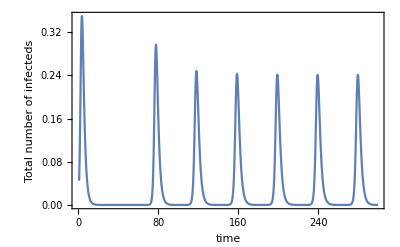

```mathematica
ListLinePlot[Transpose[{tval,IT}],PlotRange->All,Frame->True,FrameLabel->{"time", "Total number of infecteds"}]
```

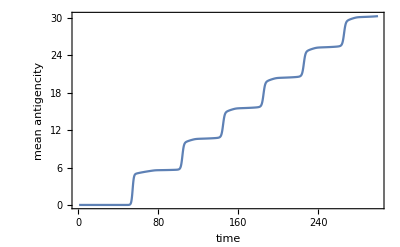

```mathematica
ListLinePlot[Transpose[{tval,ex}],PlotRange->All,Frame->True,FrameLabel->{"time", "mean antigencity"}]
```

## Oligomorphic dynamics

### Model setting

#### Model parameters

```mathematica
β=2;α=0.1;γ=0.5;S0=1;𝒟=0.001;

Clear[x];
(* cross-immunity *)
w=2;σ[x_]=Exp[-x^2/(2 w^2)];
```

#### Basic reproductive ratio

```mathematica
ρ=β/(γ+α)S0
```

3.33333

#### Final size of a single epidemic

```mathematica
ψ0=ψ/.FindRoot[ψ==1-Exp[-ρ ψ],{ψ,1-1/ρ}]
```

0.959118

### Constructing OMD for the second outbreak

#### 1. Define susceptibility profile after the first epidemic

```mathematica
(* susceptibility profile after the first epidemic *)
s[x_]=(1-ψ0)^σ[x];
```

#### 2. Obtain the minimum antigenicity distance, xc, necessary to escape the cross - immunity suppression after the first epidemic

```mathematica
(* the minimum antigenicity distance necessary to escape the cross-immunity supression after the first epidemic *)
xc=x/.FindRoot[s[x]==1/ρ,{x,3}]
```

2.79515

#### 3. Find the time where the second peak is becoming emerging and set it as the starting point for OMD

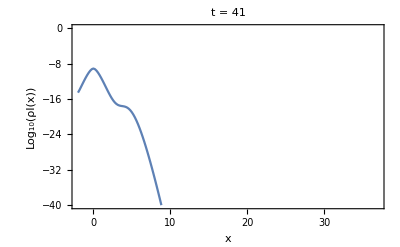

```mathematica
i0=40;
ListLinePlot[Transpose[{xval,Log10[ρI⟦i0⟧]}],PlotRange->{-40,0},PlotLabel->"t = "<>ToString[timeTR⟦i0⟧],Frame->True,FrameLabel->{"x","Log_10(ρI(x))"}]
```

```mathematica
t0=timeTR[[i0]]
```

41

#### 4. Divide the antigenicity between two antigenicity groups, those with x < xc and those with x > xc

```mathematica
ic=Select[xval,#<xc&]//Length;
(* infected density distribution and antigeniciy traits for x<xc group *)
ρI0=Take[ρI⟦i0⟧,ic];
xval0=Take[xval,ic];
(* infected density distribution and antigeniciy traits for x>xc group *)
ρI1=Take[ρI⟦i0⟧,{ic+1,Length[xval]}];
xval1=Take[xval,{ic+1,Length[xval]}];

(* total infected densities of two groups *)
I0=ρI0//Total;
I1=ρI1//Total;

(* relative proportion of two groups in infected population *)
(* THE INITIAL CONDITION FOR THE 0TH ORDER OMD *)
p0=I0/(I0+I1);
p1=I1/(I0+I1);

(* mean antigenicity within each group *)
(* THE INITIAL CONDITION FOR THE 1ST ORDER OMD *)
(* inner product of trait vector and density vector *)
ex0=xval0.ρI0/I0;
ex1=xval1.ρI1/I1;

(* variance of antigenicity within each group *)
(* THE INITIAL CONDITION FOR THE 2ND ORDER OMD *)
V0=((xval0-ex0)^2).ρI0/I0;
V1=((xval1-ex1)^2).ρI1/I1;
```

```mathematica
Print["t0 = ",t0, " xc= ",xc]
Print["Sum(I(x),x<xc)= ",I0, "\tSum(I(x),x>xc)= ",I1]
Print["p0 = ",p0,"\tp1 = ",p1]
Print["E[x|x<xc] = ",ex0,"\tE[x|x>xc] = ",ex1]
Print["V[x|x<xc] = ",V0,"\tV[x|x>xc] = ",V1]
```

t0 = 41 xc= 2.79515

Sum(I(x),x<xc)= 2.68873×10^-9	Sum(I(x),x>xc)= 4.23125×10^-17

p0 = 1.	p1 = 1.5737×10^-8

E[x|x<xc] = 3.14883×10^-7	E[x|x>xc] = 3.23948

V[x|x<xc] = 0.0927593	V[x|x>xc] = 0.267511

### Integrating OMD for the second epidemic outbreak and Compare with simulation results

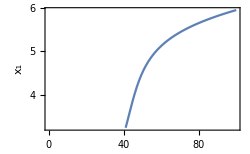

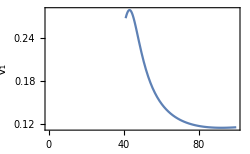

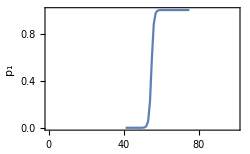

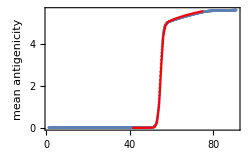

```mathematica
tend=100;
Clear[t]
ser=NDSolve[{
M'[t]==β s'[M[t]]V[t],
V'[t]==β s''[M[t]]V[t]^2+2𝒟,M[t0]==ex1,V[t0]==V1},{M,V},{t,t0,tend}];
(* Mean antigenicity of morph 1 *)
Plot[M[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","x_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}]
(* Variance in morph 1 *)
Plot[V[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","V_1"},ImageSize->250,PlotRange->{{0,tend},Automatic}]

tep=75;
(* Solution of dp1/dt = β(s(M(t))-s(X0))p1(1-p1) *)
zser=Log[p1/(1-p1)]+Table[NIntegrate[β(s[M[t]/.ser⟦1⟧]-s[ex0]),{t,t0,τ}],{τ,t0,tep}];
pser=1/(1+Exp[-zser]);
tser=Range[t0,tep];
grfp1=ListLinePlot[Transpose[{tser,pser}],PlotRange->{{0,tend},All},Frame->True,FrameLabel->{"t","p_1"},ImageSize->250]
ex1ser=Table[M[t]/.ser⟦1⟧,{t,t0,tep}];

grfA=Show[
ListPlot[Take[Transpose[{tval,ex}],900],PlotRange->All,Frame->True,FrameLabel->{"time", "mean antigencity"}],
(* ListLinePlot[Transpose[{tser,ex1ser}],PlotStyle->{Dashed,Red}], *)
ListLinePlot[Transpose[{tser,ex0(1-pser)+ex1ser pser}],PlotRange->All,PlotStyle->Red],PlotRange->All,Frame->True,FrameLabel->{"t","mean antigenicity"},Axes->None,ImageSize->250
]
```

### Save to file

```mathematica
FIGDIR="fig/";
```

```mathematica
Export[FIGDIR<>"JumpOMDFirstEX.eps",grfA];
Export[FIGDIR<>"JumpOMDFirstEX.pdf",grfA];
```

```mathematica
Export[FIGDIR<>"Jump.eps",grfB];
Export[FIGDIR<>"Jump.pdf",grfB];
```

#### 5. Predicting the waiting time from the initial condition dV/dt = a V^2 + b

```mathematica
Clear[a,X,x]
x=X/.DSolve[{X'[t]==a X[t]^2+b,X[0]==X0},X,t,Assumptions->a>0&&b>0&&X0>0]⟦1⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Function[{t},√(b/a) Tan[√(a b) t+ArcTan[(a √(b/a) X0)/b]]]

```mathematica
Tan[π/2]
```

ComplexInfinity

```mathematica
tc=t/.Solve[√(a b) t+ArcTan[(a √(b/a) X0)/b]==π/2,t]⟦1⟧
```

(π-2 ArcTan[(a √(b/a) X0)/b])/(2 √(a b))

π/4

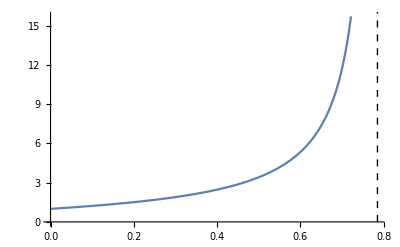

```mathematica
par={a->1,b->1,X0->1};
tc/.par
Plot[x[t]/.par,{t,0,tc/.par},Epilog->{Dashed,Line[{{tc/.par,0},{tc/.par,20}}]}]
```

```mathematica
par={a->β s''[ex1],b->2𝒟,X0->V1}
```

{a→0.11567,b→0.002,X0→0.267511}

```mathematica
t0
```

41

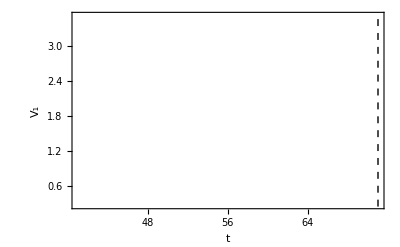

```mathematica
ParametricPlot[{t0+t,x[t]/.par},{t,0,tc/.par},Epilog->{Dashed,Line[{{t0+tc/.par,0},{t0+tc/.par,20}}]},Frame->True,FrameLabel->{"t","V_1"},AspectRatio->1/GoldenRatio]
```

Initial mean of morph 1 antigenicity

```mathematica
X0=ex1
```

3.23948

Initial frequency of morph 1

```mathematica
P0=pser//First
```

1.5737×10^-8

s(t) = s0 + k(t-t0)

```mathematica
s0=s[X0]
k=β(s'[X0])^2 V1
```

0.422699

0.0464909

Approx time to reach p1=1/2

```mathematica
tc=(Sqrt[s0^2+2k Log[1/P0]]-s0)/k
```

20.1586

```mathematica
t0+tc
```

61.1586

```mathematica
Clear[S,p,p0]
Solve[Log[p/(1-p)]-Log[p0/(1-p0)]==S,p]
```

{{p→ConditionalExpression[(ⅇ^S p0)/((1-p0) (1+(ⅇ^S p0)/(1-p0))), -π<Im[S+Log[p0/(1-p0)]]≤π]}}

```mathematica
P0
```

1.5737×10^-8

```mathematica
sa[t_]=Integrate[s0+k t,t]
```

0.422699 t+0.0232455 t^2

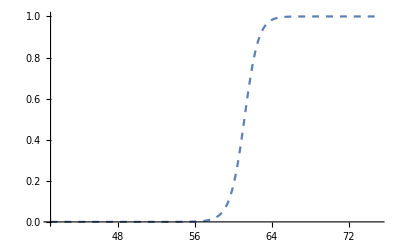

```mathematica
grfp1approx=Plot[(ⅇ^S p0)/((1-p0) (1+(ⅇ^S p0)/(1-p0)))/.{S->sa[t-t0],p0->P0},{t,t0,75},PlotRange->All,PlotStyle->{Dashed}]
```

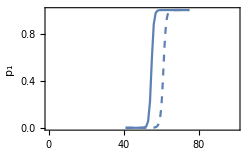

```mathematica
Show[
grfp1,
grfp1approx
]
```

```mathematica
Clear[x]
s'[x]
```

0.799265 0.0408823^(ⅇ^(-x^2/8)) ⅇ^(-x^2/8) x

```mathematica
X0
```

3.23948

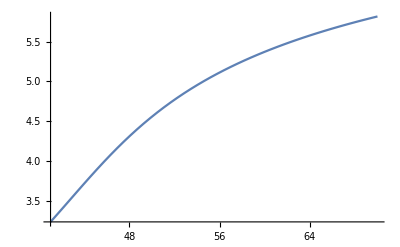

```mathematica
serx=NDSolve[{x'[t]==β s'[x[t]]V1,x[t0]==X0},x,{t,t0,70}];
Plot[x[t]/.serx,{t,t0,70}]
```

Approx antigenicity for the next outbreak

```mathematica
X0+β s'[X0]V1 tc
```

6.41878

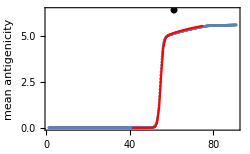

```mathematica
Show[
grfA,
Graphics[{PointSize[0.02],Point[{t0+tc,X0+β s'[X0]V1 tc}]}]
]
```

```mathematica
t0+1/(β (s[ex1]- s[ex0]))Log[1/(pser//First)]
t0+1/(β (s[5]- s[ex0]))Log[1/(pser//First)]
```

64.5286

51.8489

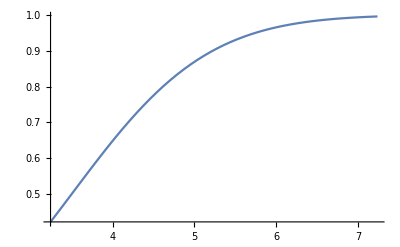

```mathematica
Plot[s[x],{x,ex1,ex1+4}]
```

## Predicting the second jump

### OMD from t = 100 (when the third peak becomes visible)

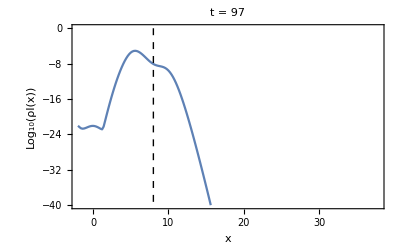

```mathematica
i=g0=96;
xc2=8;
ListLinePlot[Transpose[{xval,Log10[ρI⟦i⟧]}],PlotRange->{-40,0},PlotLabel->"t = "<>ToString[timeTR⟦i⟧],Frame->True,FrameLabel->{"x","Log_10(ρI(x))"},Epilog->{Dashed,Line[{{xc2,0},{xc2,-40}}]}]
```

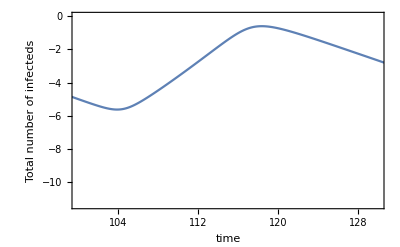

```mathematica
ListLinePlot[Transpose[{tval,Log10[IT]}],PlotRange->{{100,130},Automatic},Frame->True,FrameLabel->{"time", "Total number of infecteds"}]
```

#### Getting the initial within - morph moments

```mathematica
t0=timeTR[[g0]];
ic=Select[xval,#<xc2&]//Length;
ρI0=Take[ρI⟦g0⟧,ic];
xval0=Take[xval,ic];
ρI1=Take[ρI⟦g0⟧,{ic+1,Length[xval]}];
xval1=Take[xval,{ic+1,Length[xval]}];
I0=ρI0//Total;
I1=ρI1//Total;
p0=I0/(I0+I1);
p1=I1/(I0+I1);
ex0=xval0.ρI0/I0;
ex1=xval1.ρI1/I1;
V0=((xval0-ex0)^2).ρI0/I0;
V1=((xval1-ex1)^2).ρI1/I1;
Print["t0 = ",t0, " xc= ",xc2]
Print["Sum(I(x),x<xc)= ",I0, "\tSum(I(x),x>xc)= ",I1]
Print["p0 = ",p0,"\tp1 = ",p1]
Print["E[x|x<xc] = ",ex0,"\tE[x|x>xc] = ",ex1]
Print["V[x|x<xc] = ",V0,"\tV[x|x>xc] = ",V1]
```

t0 = 97 xc= 8

Sum(I(x),x<xc)= 0.0000451127	Sum(I(x),x>xc)= 3.17327×10^-8

p0 = 0.999297	p1 = 0.000702915

E[x|x<xc] = 5.63376	E[x|x>xc] = 8.54044

V[x|x<xc] = 0.224324	V[x|x>xc] = 0.276789

#### Susceptibility profile at t = 100

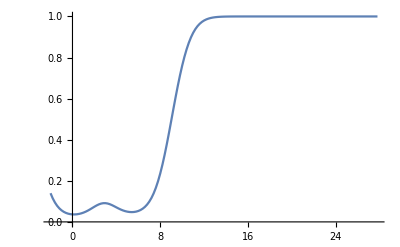

```mathematica
ListLinePlot[Take[Transpose[{xval,ρS[[g0]]}],150]]
```

```mathematica
s2=Interpolation[Take[Transpose[{xval,ρS[[g0]]}],150]]
```

InterpolatingFunction[…]

#### Comparing with simulation results

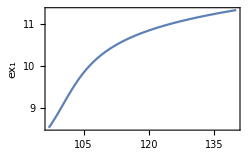

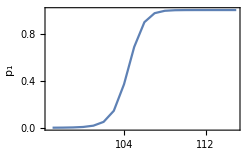

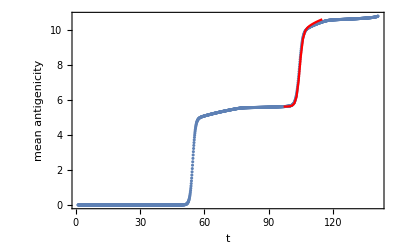

```mathematica
tend=140;
Clear[t]
ser=NDSolve[{
M'[t]==β s2'[M[t]]V[t],
V'[t]==β s2''[M[t]]V[t]^2+2𝒟,M[t0]==ex1,V[t0]==V1},{M,V},{t,t0,tend}];
Plot[M[t]/.ser,{t,t0,tend},Frame->True,FrameLabel->{"t","ex_1"},ImageSize->250]
tep=115;
zser=Log[p1/(1-p1)]+Table[NIntegrate[β(s2[M[t]/.ser⟦1⟧]-s2[ex0]),{t,t0,τ}],{τ,t0,tep}];
pser=1/(1+Exp[-zser]);
tser=Range[t0,tep];
ListLinePlot[Transpose[{tser,pser}],PlotRange->All,Frame->True,FrameLabel->{"t","p_1"},ImageSize->250]
ex1ser=Table[M[t]/.ser⟦1⟧,{t,t0,tep}];

Show[
ListPlot[Take[Transpose[{tval,ex}],1400],PlotRange->All,Frame->True,FrameLabel->{"time", "mean antigencity"}],
(* ListLinePlot[Transpose[{tser,ex1ser}],PlotStyle->{Dashed,Red}], *)
ListLinePlot[Transpose[{tser,ex0(1-pser)+ex1ser pser}],PlotRange->All,PlotStyle->Red],PlotRange->All,Frame->True,FrameLabel->{"t","mean antigenicity"},Axes->None,ImageSize->400
]
```